```mathematica
If[!NumberQ[makePallette],NotebookEvaluate[NotebookDirectory[]~~"visualVocabDefs.nb"],NotebookEvaluate[NotebookDirectory[]~~"vvClear.nb"]];
```

## Representation of Images

Digital images are made of numbers. Because numbers are hard to look at (especially when there are a lot of them), people have come up with a variety of clever ways to display them. Linear metaphors (where larger numerical values correspond to longer lines), spatial metaphors (where larger numbers correspond to greater areas), contrast metaphors (where darker regions correspond to smaller values and brighter regions correspond to larger values, or vice versa!), and color metaphors (where different hues correspond to different values) can all be combined and modified in a wonderful array of possibilities. This notebook discusses several different ways that images can be represented and displayed.

```mathematica
TableForm[{{Hyperlink["1DFunction",{"visualVocabRepresentation.nb","1D Function"}],label1DFunction},{Hyperlink["2DFunction",{"visualVocabRepresentation.nb","2D Function"}],label2DFunction},{Hyperlink["ColorPixels",{"visualVocabRepresentation.nb","Color Pixels"}],labelColorPixels},{Hyperlink["PixelSize",{"visualVocabRepresentation.nb","Pixel Size"}],labelPixelSize},{Hyperlink["RealPatch",{"visualVocabRepresentation.nb","Real Patch"}],labelRealPatch},{Hyperlink["CanvasPatch",{"visualVocabRepresentation.nb","Canvas Patch"}],labelCanvasPatch},{Hyperlink["ColorPatch",{"visualVocabRepresentation.nb","Color Patch"}],labelColorPatch},{Hyperlink["ColorChannels",{"visualVocabRepresentation.nb","Color Channels"}],labelColorChannels},{Hyperlink["ImageChannels",{"visualVocabRepresentation.nb","Image Channels"}],labelImageChannels},{Hyperlink["HSBColorSpace",{"visualVocabRepresentation.nb","HSB Color Space"}],labelHSBColorSpace},{Hyperlink["HSBChannels",{"visualVocabRepresentation.nb","HSB Channels"}],labelHSBChannels}}]
```

1DFunctionvisualVocabRepresentation.nb1D FunctionvisualVocabRepresentation.nb | Digital images are made of numbers that can be displayed in a variety of ways
2DFunctionvisualVocabRepresentation.nb2D FunctionvisualVocabRepresentation.nb | Two-dimensional data can also be represented in many ways
ColorPixelsvisualVocabRepresentation.nbColor PixelsvisualVocabRepresentation.nb | Colors are represented by combining three numbers
PixelSizevisualVocabRepresentation.nbPixel SizevisualVocabRepresentation.nb | How big is a pixel?
RealPatchvisualVocabRepresentation.nbReal PatchvisualVocabRepresentation.nb | Black is zero, white is one, and grays are in between
CanvasPatchvisualVocabRepresentation.nbCanvas PatchvisualVocabRepresentation.nb | None of the white areas are completely white: the maximum value is about 0.8
ColorPatchvisualVocabRepresentation.nbColor PatchvisualVocabRepresentation.nb | Colored pixels are triplets of numbers representing the amount of red, green, and blue in each pixel
ColorChannelsvisualVocabRepresentation.nbColor ChannelsvisualVocabRepresentation.nb | Visualizing the red, green, and blue channels as separate (grayscale) images called channels
ImageChannelsvisualVocabRepresentation.nbImage ChannelsvisualVocabRepresentation.nb | Visualizing the red (upper right), green (bottom left), and blue
(bottom right) channels as separate grayscale images
HSBColorSpacevisualVocabRepresentation.nbHSB Color SpacevisualVocabRepresentation.nb | The hue, saturation, and brightness can be changed independently in the HSB colorspace
HSBChannelsvisualVocabRepresentation.nbHSB ChannelsvisualVocabRepresentation.nb | Visualizing the hue (top right), saturation (bottom left), and brightness (bottom right) channels as separate grayscale images

There are four important functions in this notebook. Image[ ] displays numerical data in the form of an image, handles conversions between different file formats (.jpg, .tif, .gif, etc) and colorspaces (RGB, HSB), and has a number of display options such as the size at which the image will be displayed. ImageData[ ] extracts numerical data from an image so that it can be operated on using normal mathematical operations. ImageTake[ ] extracts specified rows and columns from an image. ListPLot[ ] takes a list of values and plots them.

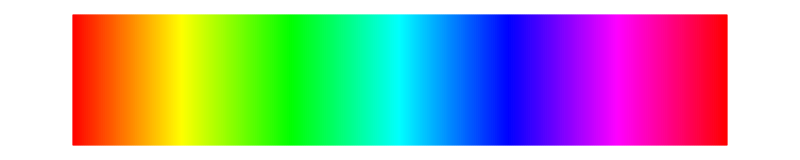

```mathematica
specLine
```

Start at the beginning, in one dimension.

```mathematica
label1DFunction="Digital images are made of numbers that can be displayed in a variety of ways";info1DFunction="Move the x-slider to change one of the function values. Observe how the various representations change.\n\nColors in such representations are arbitrary (change color schemes).\n\nImagining that the underlying data is actually continuous, there are many ways to 'connect the dots'. The smoothness chooser shows four ways.\n\nEach part shows the same data, only the method of display differs.";
pattern1D[x_]:={0,0.2,0.4,0.6,0.8,x,0.9,0.1,0.8,0.2,0.7,0.1};
Manipulate[Column[{pattern1D[x],Spacer[10],ListPlot[pattern1D[x],ColorFunction->colorScheme,Filling->Axis,PlotStyle->PointSize[0.02],FillingStyle->Thickness[0.003],PlotRange->{0,1}],Spacer[10],Rotate[ArrayPlot[Partition[pattern1D[x],1]],Pi/2],Spacer[10],Rotate[ArrayPlot[1-Partition[pattern1D[x],1]],Pi/2],Spacer[10],Rotate[MatrixPlot[Partition[pattern1D[x],1],Frame->False,ColorFunction->colorScheme],Pi/2],Spacer[10],pattFun=Interpolation[pattern1D[x],InterpolationOrder->smoothness];
Plot[pattFun[y],{y,1,Length[pattern1D[0]]},PlotRange->{{0,11},{0,1}},Filling->Axis]}],{{x,0.5},0,1,0.01},Row[{Control[{{colorScheme,"ThermometerColors","color scheme"},ColorData["Gradients"]}],Spacer[20],Control[{smoothness,{0,1,2,3}}],Spacer[20],info[info1DFunction]}],FrameLabel->Style[label1DFunction,Medium],TrackedSymbols->{x,colorScheme,smoothness},SaveDefinitions->True]
```

```mathematica
specLine
```

-Graphics-

```mathematica
label2DFunction="Two-dimensional data can also be represented in many ways";info2DFunction="Move the x-slider to change one of the function values. Observe how the various representations change.\n\nColors in such representations are arbitrary (change color schemes).\n\nEach part shows the same data, only the method of display differs.";
patternA[x_]:=Module[{},m= Partition[Range[25]-1,5]/25.;m[[3,3]]=x;m];
Manipulate[Row[{
MatrixForm[patternA[x]],Spacer[10],
ArrayPlot[patternA[x],Frame->False],Spacer[10],
ArrayPlot[1-patternA[x],Frame->False],Spacer[10],
MatrixPlot[patternA[x],Frame->False,ColorFunction->colorScheme],Spacer[10],
ListPointPlot3D[patternA[x],ImageSize->300,ColorFunction->colorScheme,Filling->Axis,PlotStyle->PointSize[0.04],FillingStyle->Thickness[0.01]],Spacer[10],
ListPlot3D[patternA[x],InterpolationOrder->2,ImageSize->300,ColorFunction->colorScheme]}],
Row[{Control[{{x,0.5},0,1,0.01}],Spacer[20],Control[{{colorScheme,"ThermometerColors","color scheme"},ColorData["Gradients"]}],Spacer[20],info[info2DFunction]}],FrameLabel->Style[label2DFunction,Medium],
TrackedSymbols->{x,colorScheme},SaveDefinitions->True]
```

```mathematica
specLine
```

-Graphics-

Color: most any color can be made up as a combination of mixtures of red, blue and green. Note that all ones gives white, all zeros give black. Other colors are different mixtures of the three. (This is different than paints where red-green-blue paints mix together give black).

```mathematica
labelColorPixels="Colors are represented by combining three numbers";infoColorPixels="Move the three sliders to change the color of the center pixel.\n\nCan you make it pure red?\n\nMake it light gray.\n\nMake it white by setting all values to one; make it black by setting all values to 0.\n\nCan you make it dark green?";Manipulate[a={{{1,0,0},{0,1,0},{0,0,1}},{{1,1,1},{r,g,b},{0,0,0}},{{1,1,0},{1,0,1},{0,1,1}}};
Row[{MatrixForm[a],Spacer[20],Image[a,ImageSize->150]}],{{r,0.49,"red"},0,1,0.01,Appearance->"Labeled"},{{g,0.51,"green"},0,1,0.01,Appearance->"Labeled"},Row[{Control[{{b,0.51,"blue"},0,1,0.01,Appearance->"Labeled"}],Spacer[20],info[infoColorPixels]}],
FrameLabel->Style[labelColorPixels,Medium],
TrackedSymbols->{r,g,b},SaveDefinitions->True]
```

Each of the triplets of {r,g,b} values that defines a color is called a pixel (short for picture element). Normally images are much larger than the small 3 by 3 example above.

```mathematica
specLine
```

-Graphics-

The next demonstration picks random colors and displays the image in two ways. On the left, the image is resized so that it is always the same physical screen size. On the right, each image pixel occupies one physical pixel on the screen. You may need to increase the slider to even see anything.

```mathematica
labelPixelSize="How big is a pixel?";infoPixelSize="A box of randomly colored pixels is displayed two ways:\n\nLeft -- the pixels are resized so that the width of the box is fixed\nRight -- each pixel occupies one screen pixel";
Manipulate[randMat=RandomVariate[UniformDistribution[{0,1}],{n,n,3}];
Row[{Image[randMat,ImageSize->300],Spacer[20],Image[randMat,ImageSize->n]}],
Row[{Control[{{n,5,"pixels on each side"},1,300,1,Appearance->"Labeled"}],info[infoPixelSize]}],
FrameLabel->Style[labelPixelSize,Medium],TrackedSymbols->{n},SaveDefinitions->True]
```

```mathematica
specLine
```

-Graphics-

Of course real images are not made of random pixels. Rather, pixels are (usually) organized so as to represent some scene, some likeness, some picture, some painting, some thing, some image of interest. Here is a small patch from an x-ray of a canvas F634 by Van Gogh. It is 100 by 100 pixels (and so contains far too many numbers to display). Pick any 10 by 10 section from this patch by moving the green shade around with the mouse and observe that the blackest areas correspond to numbers that are close to zero while the whitest areas correspond to numbers near 1.

```mathematica
labelRealPatch="Black is zero, white is one, and grays are in between";infoRealPatch="A 10x10 patch of a larger x-ray is highlighted in green. Move the patch around using the mouse.\n\nCompare the patch at its real size (middle) and enlarged for easier viewing (right). The corresponding numerical representation (a 10x10 matrix) is shown at the bottom.\n\nFind the darkest patch: what is the smallest number?\nFind the brightest patch, what is the largest number?";canvasPatch=ImageAdjust[ImageTake[Import[pathXray~~"F634Tile.tif"],100,100]];gBox=Graphics[{Green,Thickness[0.2],Opacity[0.4],Polygon[{{1,1},{1,-1},{-1,-1},{-1,1}}]},ImageSize->20];
Manipulate[Row[{Image[canvasPatch,ImageSize->200],Spacer[20],smallPatch=ImageTake[canvasPatch,100-{Clip[pt[[2]]+5,{1,99}],Clip[pt[[2]]-4,{1,99}]},{Clip[pt[[1]]-4,{1,99}],Clip[pt[[1]]+5,{1,99}]}],Spacer[20],Image[smallPatch,ImageSize->{200,200}],Spacer[20],PaddedForm[MatrixForm[ImageData[smallPatch]],{2,2}]}],Row[{info[infoRealPatch],Control[{{pt,{50,50}},Locator,LocatorAutoCreate->True,Appearance->gBox}]}],
FrameLabel->Style[labelRealPatch,Medium],TrackedSymbols->{pt},SaveDefinitions->True]
```

```mathematica
specLine
```

-Graphics-

Or we can look at any row of the canvas patch. Here are the rows plotted as a function.

```mathematica
labelCanvasPatch="Plotting the rows of an image as a function";infoCanvasPatch="Change the row to see the corresponding data plotted as a function.\n\nWhat row has the most zeros?\nWhat row has the fewest zeros?\nWhich row has the highest average value?\nWhich row has the greatest variation?";
canvasPatch=ImageAdjust[ImageTake[Import[pathXray~~"F634Tile.tif"],100,100]];
{colCanvasPatch,rowCanvasPatch}=ImageDimensions[canvasPatch];
Manipulate[tLine=threadLine[canvasPatch,rowCanvasPatch-thisRow+1];
Row[{Show[Image[canvasPatch,ImageSize->200],
Graphics[{Green,Opacity[0.4],Thickness[0.03],Line[{{0,thisRow},{colCanvasPatch,thisRow}}]}]],Spacer[20],ListLinePlot[tLine,PlotRange->{{1,colCanvasPatch},{0,1}},ImageSize->250,Filling->Axis]}],
Row[{Control[{{thisRow,50,"row number"},1,rowCanvasPatch-1,1,Appearance->"Labeled"}],info[infoCanvasPatch]}],
FrameLabel->Style[labelCanvasPatch,Medium],
TrackedSymbols->{thisRow},SaveDefinitions->True]
```

```mathematica
specLine
```

-Graphics-

When the image is in color, each of the pixel elements is a collection of three numbers representing the amount of red, green, and blue components.

```mathematica
labelColorPatch="Colored pixels are triplets of numbers representing the amount of red, green, and blue in each pixel";infoColorPatch="A 6x6 patch of a color image is highlighted in green. Move the patch around using the mouse.\n\nCompare the patch at its real size (middle) and enlarged for easier viewing (right). The corresponding numerical representation (a 6x6 matrix, where each element is a RGB triplet) is shown at the bottom.\n\nRecall that pure yellow is (1,1,0). Find the yellowest patch. How close is the numerical representation to pure yellow?\n\nIn brush stroke 3, find the reddest patch. How close is the numerical representation to pure red? What is the reddest number?";gBox=Graphics[{Green,Thickness[0.2],Opacity[0.4],Polygon[{{1,1},{1,-1},{-1,-1},{-1,1}}]},ImageSize->12];
Manipulate[patch=ImageAdjust[ImageTake[allImagesColor[[vanGoghStrokes-1+stroke]],{100,200},{100,200}]];
Row[{Image[patch,ImageSize->200],Spacer[20],smallPatch=ImageTake[patch,100-{Clip[pt[[2]]+3,{1,99}],Clip[pt[[2]]-2,{1,99}]},{Clip[pt[[1]]-2,{1,99}],Clip[pt[[1]]+3,{1,99}]}],Spacer[20],Image[smallPatch,ImageSize->{200,200}],Spacer[20],PaddedForm[MatrixForm[ImageData[smallPatch]],{2,2}]}],Row[{Control[{{stroke,1,"brush stroke"},{1,2,3}}],Spacer[20],info[infoColorPatch]}],{{pt,{50,50}},Locator,LocatorAutoCreate->True,Appearance->gBox},
FrameLabel->Style[labelColorPatch,Medium],
TrackedSymbols->{stroke, pt},SaveDefinitions->saveDef]
```

```mathematica
specLine
```

-Graphics-

So far, we have been thinking of a color image as a collection of colored pixels, each of which is represented as a triplet of values representing the red, green, and blue proportions. An equivalent way of looking at a color image is to rearrange the numbers so that all the red values form one “image,” all the green values form a second image, and all the blue values form a third image. These three images can be visualized as three separate grayscale images. Here is a set of nine blocks, eight have fixed colors; the color of the center block can be changed with the sliders. The structure of the three images is shown explicitly.

```mathematica
labelColorChannels="Visualizing the red, green, and blue channels as separate (grayscale) images called channels";infoColorChannels="An equivalent way of looking at a color image is to rearrange the numbers so that all the red values form one matrix, all the green values form a second matrix, and all the blue values form a third matrix.\n\nIf these matrices are represented as grayscale images, they are called the red, green and blue channels.\n\nChange the values of the middle pixel and observe how the three channels can be viewed as three separate grayscale images.\n\nObserve that the bottom row of colors demonstrate that red+green=yellow, that red+blue=magenta, and that green+blue=cyan.";
Manipulate[a={{{1,0,0},{0,1,0},{0,0,1}},{{1,1,1},{r,g,b},{0,0,0}},{{1,1,0},{1,0,1},{0,1,1}}};
aSep=Map[ImageData,ColorSeparate[Image[a]]];
GraphicsGrid[{{MatrixForm[a],MatrixForm[aSep[[1]]],MatrixForm[aSep[[2]]],MatrixForm[aSep[[3]]]},{Image[a,ImageSize->50],Image[aSep[[1]]],Image[aSep[[2]]],Image[aSep[[3]]]}},ImageSize->600],{{r,0.49,"red"},0,1,0.01,Appearance->"Labeled"},
{{g,0.51,"green"},0,1,0.01,Appearance->"Labeled"},
Row[{Control[{{b,0.51,"blue"},0,1,0.01,Appearance->"Labeled"}],Spacer[20],info[infoColorChannels]}],
FrameLabel->Style[labelColorChannels,Medium],
TrackedSymbols->{r,g,b},SaveDefinitions->True]
```

```mathematica
specLine
```

-Graphics-

Real images can also be decomposed into their red, green, and blue components. Each of the images in the menu are shown four ways: the original image on the top left, the red channel on the top right, green channel on the bottom left and the blue channel on the bottom right. A bit of thought shows the meaning of the images: when the image is blue (as in the sky behind the church, the red and green components are black (indicating very little of these colors) while the blue channel is nearly white (indicating a large proportion of blue). A portion with considerable yellow shows strong whites in both the red and green channels and almost nothing in the blue channel (remember that red+green=yellow when mixing light).

```mathematica
labelImageChannels="Visualizing the red (upper right), green (bottom left), and blue\n(bottom right) channels as separate grayscale images";infoImageChannels="Visualizing the RGB channels as separate grayscale images.\n\nExplain why the bed frame in the bottom right image in the Bedroom at Arles is so dark.\n\nExplain why the sky in the Wheat Field is dark in the top right and bottom left images.";
Manipulate[img=Image[allImagesColor[[i]],ImageSize->300];
{imgR,imgG,imgB}=ColorSeparate[img];
Column[{Row[{img,Spacer[10],imgR}],Spacer[10],Row[{imgG,Spacer[10],imgB}]}],
Row[{Control[{{i,vanTreeRoots,"image"},Thread[Range[numFilesC]->imageNamesC],ControlType->PopupMenu}],Spacer[20],info[infoImageChannels]}],
FrameLabel->Style[labelImageChannels,Medium],TrackedSymbols->{i},SaveDefinitions->saveDef]
```

HW: Create a program that changes the color of an image with the following logic: if the R pixel is larger than both the B and G pixels, swap the R and B pixel values. Apply this function to some images and explain what you see.

```mathematica
(* Image[ImageData[img]/.{r_,g_,b_}/;r>g&&r>b->{b,g,r}] *)
```

```mathematica
specLine
```

-Graphics-

The red-green-blue RGB representation (called the RGB colorspace) is just one of the many possibilities. Another representation that sometimes comes in useful is the hue-saturation-brightness (HSB colorspace). In this representation, the hue (around the color wheel) is separated from the saturation (amount of color) and from the brightness (the grayscale version of the original image). The hue is a number from 0 to 1 where zero represents red (at the left) 0.1 is yellowish, 0.3 is greenish, 0.5 becomes blue, 0.7 is purple, and back to red at 1.

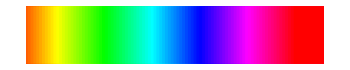
-Graphics-
{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

```mathematica
Column[{Graphics[Table[{Hue[i],Thickness[0.1],Line[{{i,0},{i,0.05}}]},{i,0,1,0.01}],ImageSize->350],Table[i,{i,0,1,0.1}]}]
```

The images in the next illustration have a variety of color schemes. Playing with the sliders should give an idea of the effect of changing the hue, saturation, and brightness. The hue slider changes purely the spectral aspects of the color, rotating through the color wheel (or moving along the rainbow-like graphic above). The saturation slider removes color as it is turned to the left, and increases the vibrancy as it is slid to the right. The brightness slider turns the image black at the left, and extra-bright at the right.

```mathematica
labelHSBColorSpace="The hue, saturation, and brightness can be changed independently in the HSB colorspace";infoHSBColorSpace="Change the hue value and observe the color\n\nChange the saturation slider (left=grayscale, right=intense colors)\n\nChange the brightness slider (left=too dark, right=too light).\n\nWhat kinds of uses can you envision for each of these controls?";
Manipulate[iHSB=ImageData[ColorConvert[allImagesColor[[i]],"HSB"],Interleaving->False];
Image[Transpose[fHSB[iHSB,h,s,b],{3,1,2}],ColorSpace->"HSB",ImageSize->500],
{{i,vanTreeRoots,"image"},Thread[Range[numFilesC]->imageNamesC],ControlType->PopupMenu},
{{h,0,"hue"},-.5,.5},
{{s,1,"saturation"},0,2},
Row[{Control[{{b,1,"brightness"},0,2}],Spacer[20],info[infoHSBColorSpace]}],
FrameLabel->Style[labelHSBColorSpace,Medium],
TrackedSymbols->{i,h,s,b},SaveDefinitions->saveDef,Initialization:>(fHSB[x_,h_,s_,b_]:={Mod[x[[1]]+h,1],s x[[2]],b x[[3]]})]
```

```mathematica
specLine
```

-Graphics-

Here is how the various images appear when decomposed into their HSB components. Each of the images in the menu are shown four ways: the original image on the top left, the hue channel on the top right, saturation channel on the bottom left, and the brightness channel on the bottom right. For example, in the bedroom scene, the hue is mostly black, because there is a large amount of “red”, in both the bed and the flooring. The saturation is brightest on the bed frame and dullest on the far wall. The brightness is effectively the grayscale version of the scene.

```mathematica
labelHSBChannels="Visualizing the hue (top right), saturation (bottom left), and brightness (bottom right) channels as separate grayscale images";infoHSBChannels="Visualizing the HSB channels as separate grayscale images.\n\nExplain why the upper right image on the Sunflowers is almost black.\n\nIn the Milkmaid, explain why the wall in the saturation image is dark while the face is light.\n\nObserve that the brightness channel is effectvely the grayscale version of the original image.";
Manipulate[img=Image[allImagesColor[[i]],ImageSize->350];
{imgH,imgS,imgB}=ColorSeparate[img,"HSB"];
Column[{Row[{img,Spacer[10],imgH}],Spacer[10],Row[{imgS,Spacer[10],imgB}]}],Row[{Control[{{i,vanTreeRoots,"image"},Thread[Range[numFilesC]->imageNamesC],ControlType->PopupMenu}],Spacer[20],info[infoHSBChannels]}],
FrameLabel->Style[labelHSBChannels,Medium],TrackedSymbols->{i},SaveDefinitions->saveDef]
```

Exercise: Because images are just numbers, they can be created from functions. Create a synthetic image consisting of three sinusoids, one vertical, one horizontal and one at 45°. (a) Display the three images separately as grayscale images. (b) Create a color image by assigning the horizontal sinusoidal image to the R channel, the vertical to the G channel and the angled to the B channel. Display the image. (Hint: use ColorCombine[ ]) (c) Assign the horizontal sinusoid to the H channel, the vertical to the S channel and the angled to the B channel and display the image. (d) Make your image interactive by creating sliders to change the frequency of the three sinusoids. (e) Make it interactive by creating a slider to change the angle of the third sinusoid.

A detailed answer to this exercise is given here.

HW: Create a synthetic image consisting of three parabolas, one vertical, one horizontal and one at 45°. (a) Display the three images separately as grayscale images. (b) Create a color image by assigning the horizontal sinusoidal image to the R channel, the vertical to the G channel and the angled to the B channel. Display the image. (Hint: use ColorCombine[ ]) (c) Assign the horizontal sinusoid to the H channel, the vertical to the S channel and the angled to the B channel and display the image. (d) Make your image interactive by creating sliders to change the exponent n in the parabola y=x^n.

HW: The sinusoidal synthetic images in the previous HW problem contain a series of black bands. Propose and implement a function that will remove the black bands, while still retaining the striped character of the sinusoids.

HW: (An unfortunate inconsistency) Think about plotting a point {x,y} in Cartesian coordinates. One normally starts at the origin, counts over x units (to the right for positive values x) and up y units (for positive values of y). Thinking of this discretely, an integer-valued point {x,y} lies in the xth column and in the yth row. Now think about a matrix. The {n,m} location in a matrix is the nth row and mth column, and the row is counted from the top down (for example, the third row is the third from the top). Thus we have two competing ways of plotting: the Cartesian way (where the origin is at the bottom/left) and the matrix way (where the origin is at the top/right). Which way is used for images? (a) Read in a grayscale image. Look at the value of pixel {5,7} using ImageValue[]. (b) Use ImageData[ ] to turn the picture into a matrix. What is the value of the {5,7} entry in this matrix? (c) Calculate the location in the ImageData matrix where the pixel value in (a) is located. (d) Calculate the location in the image where the {5,7} entry of the matrix is located.